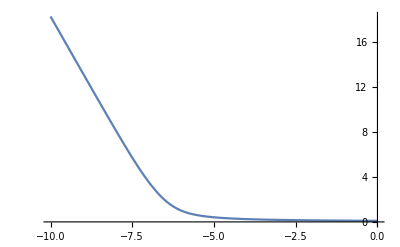

```mathematica
time[R_,r_,s_]:=If[r>R,Log[1+R/s]/Log[1+r/s],1+(Log[1+s/r]/Log[1+s/R]-1)(R Log[1+s/R])/(s Log[1+R/s])]
Plot[time[10^(-6),10^x,10^(-6.5)],{x,-10,0}]
```

```mathematica
N[Round[time[10^(-6),3.85*10^(-10),10^(-6.5)],5/800]]*1571.194762684125
```

24000.

```mathematica
Rval=Rationalize[10^(-2.25),0];
U=Rationalize[9*0.000000000225,0];
Pu=Rationalize[0.0115,0];
Am=Rationalize[0.00235,0];
Cf=Rationalize[0.0765,0];

NSolve[a/time[Rval,Cf,s]==200&&a/time[Rval,Pu,s]==40&&a>0&&s>0,{a,s},Reals]
```

{{a→20.2287,s→0.0803069}}

```mathematica
power[r_]:=a/time[Rval,r,s]/.{a->20.228691388504586,s->0.08030689931812957}
power[U]
power[Pu]
power[Am]
power[Cf]
```

1.24251

40.

10.8608

200.

```mathematica
Rval=Rationalize[10^(-3),0];
Th=Rationalize[9*0.0000000000715,0];
U=Rationalize[9*0.000000000385,0];
U238=Rationalize[9*0.000000000225,0];
Np=Rationalize[9*0.00000047,0];
Pu=Rationalize[9*0.0000027,0];
Am=Rationalize[9*0.00014,0];
Cm=Rationalize[9*0.000215,0];
Bk=Rationalize[9*0.000725,0];
Cf=Rationalize[9*0.38,0];

NSolve[a/time[Rval,Cf,s]==1000&&a/time[Rval,U238,s]==1&&a>0&&s>0,{a,s},Reals]
```

{{a→984.059,s→6.88924×10^-222},{a→416.266,s→3.03463×10^-6},{a→14.5831,s→0.0115497}}

```mathematica
power[r_]:=a/time[Rval,r,s]/.{a->14.583050873933418,s->0.011549670717287637}
power[Th]
power[U]
power[U238]
power[Np]
power[Pu]
power[Am]
power[Cm]
power[Bk]
power[Cf]
```

0.924242

1.03994

1.

2.20531

3.04347

18.1843

27.203

78.6523

1000.